```mathematica
(*图a的裸结果*)
gpda=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-a-p-newda-4D.wdx"];
aHdg=Query[1,1]@gpda;
aHer=Query[1,2]@gpda;
aHda=Query[1,3]@gpda;
aEdg=Query[2,1]@gpda;
aEer=Query[2,2]@gpda;
aEda=Query[2,3]@gpda;
aHdgf=Interpolation[Flatten[aHdg,1]];
aHerf=Interpolation[Flatten[aHer,1]];
aHdaf=Interpolation[Flatten[aHda,1]];
aEdgf=Interpolation[Flatten[aEdg,1]];
aEerf=Interpolation[Flatten[aEer,1]];
aEdaf=Interpolation[Flatten[aEda,1]];
(*pi+,只需要乘上系数*)
ap1=(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
ap1Hdg[x_,t_]=ap1*aHdgf[x,t];
ap1Her[x_,t_]=ap1*aHerf[x,t];
ap1Hda[x_,t_]=ap1*aHdaf[x,t];
ap1Edg[x_,t_]=ap1*aEdgf[x,t];
ap1Eer[x_,t_]=ap1*aEerf[x,t];
ap1Eda[x_,t_]=ap1*aEdaf[x,t];
(*pi+的u贡献，分段但就是总的*)
ap1Hdgre[x_,t_]=ap1Hdg[x,t];
ap1Herre[x_,t_]=ap1Hda[x,t]+ap1Her[x,t];
ap1Edgre[x_,t_]=ap1Edg[x,t];
ap1Eerre[x_,t_]=ap1Eda[x,t]+ap1Eer[x,t];

(*pi0,先系数再多一个来自input的1/2，求和之后整体反转*)
ap0=(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
ap0Hdg[x_,t_]=ap0*aHdgf[x,t];
ap0Her[x_,t_]=ap0*aHerf[x,t];
ap0Hda[x_,t_]=ap0*aHdaf[x,t];
ap0Edg[x_,t_]=ap0*aEdgf[x,t];
ap0Eer[x_,t_]=ap0*aEerf[x,t];
ap0Eda[x_,t_]=ap0*aEdaf[x,t];
(*pi0的u，之后要和反转的求和*)
ap0Hdgre1[x_,t_]=ap0Hdg[x,t];
ap0Herre1[x_,t_]=ap0Hda[x,t]+ap0Her[x,t];
ap0Edgre1[x_,t_]=ap0Edg[x,t];
ap0Eerre1[x_,t_]=ap0Eda[x,t]+ap0Eer[x,t];
(*反转*)
ap0Hdgre0[x_,t_]=-ap0Hdgre1[-x,t];
ap0Herre0[x_,t_]=-ap0Herre1[-x,t];
ap0Edgre0[x_,t_]=-ap0Edgre1[-x,t];
ap0Eerre0[x_,t_]=-ap0Eerre1[-x,t];
(*求和,只有erbl要加起来，以及画图也是分段那其实只要算erbl*)
ap0Herre[x_,t_]=ap0Herre1[x,t]+ap0Herre0[x,t];
ap0Eerre[x_,t_]=ap0Eerre1[x,t]+ap0Eerre0[x,t];
(*图a的总结果，就是对粒子求和*)
aHdgzall[x_,t_]=ap1Hdgre[x,t]+ap0Hdgre1[x,t];
aHdgfall[x_,t_]=ap0Hdgre0[x,t];
aHerall[x_,t_]=ap1Herre[x,t]+ap0Herre[x,t];
aEdgzall[x_,t_]=ap1Edgre[x,t]+ap0Edgre1[x,t];
aEdgfall[x_,t_]=ap0Edgre0[x,t];
aEerall[x_,t_]=ap1Eerre[x,t]+ap0Eerre[x,t];


(*图k,l的裸结果*)
gpdkl=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-kl-p-newda-4D.wdx"];
kHda=Query[1,3]@gpdkl;
lEda=Query[2,3]@gpdkl;
kHdaf=Interpolation[Flatten[kHda,1]];
lEdaf=Interpolation[Flatten[lEda,1]];
(*k,l的系数*)
kp=1/(4*2*(0.093)^2*(2Pi)^4);
lp=2*(1.24+0.46)/(2*(0.093)^2*(2Pi)^4);
kpHda[x_,t_]=kp*kHdaf[x,t];
lpEda[x_,t_]=lp*lEdaf[x,t];
(*总结果只有ERBL*)
kpHall[x_,t_]=kpHda[x,t];
lpEall[x_,t_]=lpEda[x,t];



(*图m的裸结果*)
gpdm=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-m-p-newda-4D.wdx"];
mHdg=Query[1,1]@gpdm;
mHer=Query[1,2]@gpdm;
mHda=Query[1,3]@gpdm;
mEdg=Query[2,1]@gpdm;
mEer=Query[2,2]@gpdm;
mEda=Query[2,3]@gpdm;
mHdgf=Interpolation[Flatten[mHdg,1]];
mHerf=Interpolation[Flatten[mHer,1]];
mHdaf=Interpolation[Flatten[mHda,1]];
mEdgf=Interpolation[Flatten[mEdg,1]];
mEerf=Interpolation[Flatten[mEer,1]];
mEdaf=Interpolation[Flatten[mEda,1]];
(*pi+,只需要乘上系数*)
mp1=(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
mp1Hdg[x_,t_]=mp1*mHdgf[x,t];
mp1Her[x_,t_]=mp1*mHerf[x,t];
mp1Hda[x_,t_]=mp1*mHdaf[x,t];
mp1Edg[x_,t_]=mp1*mEdgf[x,t];
mp1Eer[x_,t_]=mp1*mEerf[x,t];
mp1Eda[x_,t_]=mp1*mEdaf[x,t];
(*pi+的u贡献，分段但就是总的*)
mp1Hdgre[x_,t_]=mp1Hdg[x,t];
mp1Herre[x_,t_]=mp1Hda[x,t]+mp1Her[x,t];
mp1Edgre[x_,t_]=mp1Edg[x,t];
mp1Eerre[x_,t_]=mp1Eda[x,t]+mp1Eer[x,t];

(*pi0,先系数，求和之后整体反转*)
mp0=(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
mp0Hdg[x_,t_]=mp0*mHdgf[x,t];
mp0Her[x_,t_]=mp0*mHerf[x,t];
mp0Hda[x_,t_]=mp0*mHdaf[x,t];
mp0Edg[x_,t_]=mp0*mEdgf[x,t];
mp0Eer[x_,t_]=mp0*mEerf[x,t];
mp0Eda[x_,t_]=mp0*mEdaf[x,t];
(*pi0的u，之后要和反转的求和*)
mp0Hdgre1[x_,t_]=mp0Hdg[x,t];
mp0Herre1[x_,t_]=mp0Hda[x,t]+mp0Her[x,t];
mp0Edgre1[x_,t_]=mp0Edg[x,t];
mp0Eerre1[x_,t_]=mp0Eda[x,t]+mp0Eer[x,t];
(*反转*)
mp0Hdgre0[x_,t_]=-mp0Hdgre1[-x,t];
mp0Herre0[x_,t_]=-mp0Herre1[-x,t];
mp0Edgre0[x_,t_]=-mp0Edgre1[-x,t];
mp0Eerre0[x_,t_]=-mp0Eerre1[-x,t];
(*反转之后求和,只有erbl要加起来，以及画图也是分段那其实只要算erbl*)
mp0Herre[x_,t_]=mp0Herre1[x,t]+mp0Herre0[x,t];
mp0Eerre[x_,t_]=mp0Eerre1[x,t]+mp0Eerre0[x,t];

(*pi-,只需要乘上系数*)
mp11=(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
mp11Hdg[x_,t_]=mp11*mHdgf[x,t];
mp11Her[x_,t_]=mp11*mHerf[x,t];
mp11Hda[x_,t_]=mp11*mHdaf[x,t];
mp11Edg[x_,t_]=mp11*mEdgf[x,t];
mp11Eer[x_,t_]=mp11*mEerf[x,t];
mp11Eda[x_,t_]=mp11*mEdaf[x,t];
(*pi-的u贡献,ubar的反转*)
mp11Hdgre0[x_,t_]=mp11Hdg[x,t];
mp11Herre0[x_,t_]=mp11Hda[x,t]+mp11Her[x,t];
mp11Edgre0[x_,t_]=mp11Edg[x,t];
mp11Eerre0[x_,t_]=mp11Eda[x,t]+mp11Eer[x,t];
(*最后结果*)
mp11Hdgre[x_,t_]=-mp11Hdgre0[-x,t];
mp11Herre[x_,t_]=-mp11Herre0[-x,t];
mp11Edgre[x_,t_]=-mp11Edgre0[-x,t];
mp11Eerre[x_,t_]=-mp11Eerre0[-x,t];
(*图m的总结果*)
mHdgzall[x_,t_]=mp1Hdgre[x,t]+mp0Hdgre1[x,t];
mHdgfall[x_,t_]=mp0Hdgre0[x,t]+mp11Hdgre[x,t];
mHerall[x_,t_]=mp1Herre[x,t]+mp0Herre[x,t]+mp11Herre[x,t];
mEdgzall[x_,t_]=mp1Edgre[x,t]+mp0Edgre1[x,t];
mEdgfall[x_,t_]=mp0Edgre0[x,t]+mp11Edgre[x,t];
mEerall[x_,t_]=Re[mp1Eerre[x,t]+mp0Eerre[x,t]+mp11Eerre[x,t]];
```

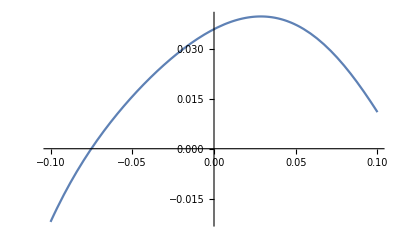

```mathematica
Plot[mHerall[x,-1],{x,-0.1,0.1}]
```

```mathematica
(*全部的总结果*)
```

```mathematica
Hdgz[x_,t_]=x*aHdgzall[x,t]+x*mHdgzall[x,t];
Her[x_,t_]=x*aHerall[x,t]+x*kpHall[x,t]+x*mHerall[x,t];
Hdgf[x_,t_]=x*aHdgfall[x,t]+x*mHdgfall[x,t];
Edgz[x_,t_]=x*aEdgzall[x,t]+x*mEdgzall[x,t];
Eer[x_,t_]=x*aEerall[x,t]+x*lpEall[x,t]+x*mEerall[x,t];
Edgf[x_,t_]=x*aEdgfall[x,t]+x*mEdgfall[x,t];
```

```mathematica
Plot3D[Hdgz[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All,AxesLabel->{"x","t","xH(x,t)"}]
```

-Graphics3D-

```mathematica
pH=Show[Plot3D[Hdgz[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[Hdgf[x,t],{x,-1,-0.1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[Her[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","xH^u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pE=Show[Plot3D[Edgz[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[Edgf[x,t],{x,-1,-0.1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[Eer[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","x E^u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {0.108036,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.112054,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
pathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Hu-0.1.pdf"}];
pathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Eu-0.1.pdf"}];
```

```mathematica
Export[pathH,pH]
```

G:\calc-online\gpd\3dre\Hu-0.1.pdf

```mathematica
Export[pathE,pE]
```

G:\calc-online\gpd\3dre\Eu-0.1.pdf

```mathematica
Hdgz1[x_,t_]=Hdgz[x,-t];
Her1[x_,t_]=Her[x,-t];
Hdgf1[x_,t_]=Hdgf[x,-t];
Edgz1[x_,t_]=Edgz[x,-t];
Eer1[x_,t_]=Eer[x,-t];
Edgf1[x_,t_]=Edgf[x,-t];
```

```mathematica
pH1=Show[Plot3D[Hdgz1[x,t],{x,0.1,1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Hdgf1[x,t],{x,-1,-0.1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Re[Her1[x,t]],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],AxesLabel->{"x","-t(GeV^2)","xH^u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {0.100064,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.999936,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

InterpolatingFunction::dmval: Input value {0.100064, -0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.999936,0.999931} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
pE1=Show[Plot3D[Re[Edgz1[x,t]],{x,0.1,1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Re[Edgf1[x,t]],{x,-1,-0.1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Re[Eer1[x,t]],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],AxesLabel->{"x","-t(GeV^2)","x E^u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {0.100064,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.999936,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
pathH1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Hufanzhuan-0.1-newda.pdf"}];
pathE1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Eufanzhuan-0.1-newda.pdf"}];
```

```mathematica
Export[pathH1,pH1]
Export[pathE1,pE1]
```

G:\calc-online\gpd\3dre\Hufanzhuan-0.1-newda.pdf

G:\calc-online\gpd\3dre\Eufanzhuan-0.1-newda.pdf

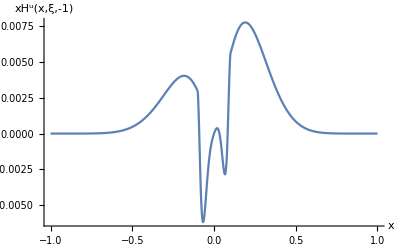

```mathematica
Show[Plot[Hdgz[x,-1],{x,0.1,1},PlotRange->All],Plot[Hdgf[x,-1],{x,-1,-0.1},PlotRange->All],Plot[Re[Her[x,-1]],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","xH^u(x,ξ,-1)"},LabelStyle->Directive[Black,Thick,12]]
```

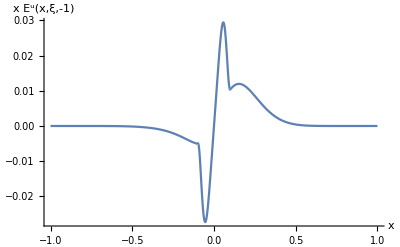

```mathematica
Show[Plot[Re[Edgz1[x,1]],{x,0.1,1},PlotRange->All],Plot[Re[Edgf1[x,1]],{x,-1,-0.1},PlotRange->All],Plot[Re[Eer1[x,1]],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","x E^u(x,ξ,-1)"},LabelStyle->Directive[Black,Thick,12]]
```

```mathematica
Re[Eer1[-0.055,1]]
```

-0.0272846

```mathematica
Re[Her[-0.07,-1]]
```

-0.0060797